```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull}

```mathematica
allGraphs6Bis=Get["d:\\Saved\\Complete6bbb.m"];
```

```mathematica
Keys[allGraphs6Bis[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofourgenerator}

```mathematica
Has
```

```mathematica
Table[
Length[Select[ListofVars[allGraphs6Bis[k,"colofourgenerator"]],SymbolLevel[#]==4&]]
,{k,Keys[allGraphs6Bis]}]//Tally//Sort
```

{{0,469},{1,2160},{2,3915},{3,4995},{4,5895},{5,5022},{6,3435},{7,3285},{8,2400},{9,2850},{10,2940},{11,1090},{12,960},{13,1110},{14,2070},{15,1260},{16,1005},{17,540},{18,1245},{19,1280},{20,600},{21,180},{22,765},{23,495},{24,690},{25,348},{27,240},{29,180},{30,465},{31,315},{32,60},{34,60},{37,20},{38,60},{42,180},{43,15},{46,60},{49,60},{51,45},{53,90},{55,30},{64,65},{65,122}}

```mathematica
def=Select[Keys[allGraphs6Bis],
Length[Select[ListofVars[allGraphs6Bis[#,"colofour"]],SymbolLevel[#]==4&&HasQuadrilateralPattern[SymbolToSets[#]]&]]>=5&];
```

```mathematica
Length[def]
```

13152

```mathematica
Select[def,With[{vars=Select[ListofVars[allGraphs6Bis[#,"colofour"]],SymbolLevel[#]==4&]},
Length[DeleteDuplicates[Select[Map [WhichQuadrilateralPattern[SymbolToSets[#]]&,vars],#≥0&]]]==5
]&]
```

{0,4782969,4960116,5019165,5038848,5039577,5039820,5039847,5039856,5039829,5039832,5039830,5039823,5039821,5039604,5039613,5039586,5039589,5039587,5039580,5039578,5040333,5040576,5040585,5040342,5039091,5039118,5039127,5039130,5039128,5039121,5039119,5039100,5039103,5039104,5039105,5039101,5039094,5039095,5039092,5039093,5038875,5038884,5038887,5038885,5038878,5038876,5038857,5038860,5038861,5038862,5038858,5038851,5038852,5038849,5038850,5019894,5020137,5020164,5020173,5020146,5020149,5020147,5020140,5020138,5019921,5019930,5019903,5019906,5019904,5019897,5019895,5020623,5020866,5020875,5020632,5019408,5019435,5019444,5019447,5019445,5019438,5019436,5019417,5019420,5019421,5019422,5019418,5019411,5019412,5019409,5019410,5019192,5019201,5019204,5019202,5019195,5019193,5019174,5019177,5019178,5019179,5019175,5019168,5019169,5019166,5019167,5078944,5098627,5098870,5098879,5098636,5079187,5079196,5078953,4979799,4980528,4980771,4980798,4980807,4980810,4980808,4980801,4980799,4980828,4980837,4980780,4980783,4980784,4980781,4980774,4980775,4980772,4980555,4980564,4980567,4980565,4980558,4980556,4980582,4980591,4980537,4980540,4980541,4980538,4980531,4980532,4980529,4980042,4980069,4980078,4980081,4980082,4980085,4980079,4980072,4980073,4980075,4980070,4980051,4980054,4980055,4980052,4980045,4980046,4980043,4979826,4979835,4979838,4979839,4979836,4979829,4979830,4979827,4979808,4979811,4979812,4979815,4979809,4979802,4979803,4979805,4979800,4960845,4961088,4961115,4961124,4961127,4961125,4961118,4961116,4961097,4961100,4961101,4961098,4961091,4961092,4961089,4960872,4960881,4960884,4960882,4960875,4960873,4960854,4960857,4960858,4960855,4960848,4960849,4960846,4960359,4960386,4960395,4960398,4960399,4960402,4960396,4960389,4960390,4960392,4960387,4960416,4960425,4960368,4960371,4960372,4960369,4960362,4960363,4960360,4960143,4960152,4960155,4960156,4960153,4960146,4960147,4960144,4960170,4960179,4960125,4960128,4960129,4960132,4960126,4960119,4960120,4960122,4960117,4842018,4861701,4862430,4862673,4862700,4862709,4862682,4862685,4862683,4862676,4862674,4862457,4862466,4862439,4862442,4862440,4862433,4862431,4863186,4863429,4863438,4863195,4861944,4861971,4861980,4861983,4861981,4861974,4861972,4861953,4861956,4861957,4861954,4861947,4861948,4861945,4861728,4861737,4861740,4861738,4861731,4861729,4861710,4861713,4861714,4861711,4861704,4861705,4861702,4842747,4842990,4843017,4843026,4842999,4843002,4843000,4842993,4842991,4842774,4842783,4842756,4842759,4842757,4842750,4842748,4843476,4843719,4843728,4843485,4842261,4842288,4842297,4842300,4842298,4842291,4842289,4842270,4842273,4842274,4842271,4842264,4842265,4842262,4842045,4842054,4842057,4842055,4842048,4842046,4842027,4842030,4842031,4842028,4842021,4842022,4842019,4901796,4921479,4921722,4921731,4921488,4902039,4902048,4901805,4802652,4803381,4803624,4803651,4803660,4803663,4803661,4803654,4803652,4803681,4803690,4803633,4803636,4803637,4803634,4803627,4803628,4803625,4803408,4803417,4803420,4803418,4803411,4803409,4803435,4803444,4803390,4803393,4803394,4803391,4803384,4803385,4803382,4802895,4802922,4802931,4802934,4802935,4802938,4802932,4802925,4802926,4802928,4802923,4802904,4802907,4802908,4802909,4802905,4802898,4802899,4802896,4802897,4802679,4802688,4802691,4802692,4802689,4802682,4802683,4802680,4802661,4802664,4802665,4802666,4802668,4802662,4802655,4802656,4802658,4802653,4802654,4783698,4783941,4783968,4783977,4783980,4783978,4783971,4783969,4783950,4783953,4783954,4783951,4783944,4783945,4783942,4783725,4783734,4783737,4783735,4783728,4783726,4783707,4783710,4783711,4783708,4783701,4783702,4783699,4783212,4783239,4783248,4783251,4783252,4783255,4783249,4783242,4783243,4783245,4783240,4783269,4783278,4783221,4783224,4783225,4783226,4783222,4783215,4783216,4783213,4783214,4782996,4783005,4783008,4783009,4783006,4782999,4783000,4782997,4783023,4783032,4782978,4782981,4782982,4782983,4782985,4782979,4782972,4782973,4782975,4782970,4782971,177147,236196,255879,256608,256851,256878,256887,256860,256863,256861,256854,256852,256635,256644,256617,256620,256618,256611,256609,256122,256149,256158,256161,256159,256152,256150,256131,256134,256135,256136,256132,256125,256126,256123,256124,255906,255915,255918,255916,255909,255907,255888,255891,255892,255893,255889,255882,255883,255880,255881,236925,237168,237195,237204,237177,237180,237178,237171,237169,236952,236961,236934,236937,236935,236928,236926,236439,236466,236475,236478,236476,236469,236467,236448,236451,236452,236453,236449,236442,236443,236440,236441,236223,236232,236235,236233,236226,236224,236205,236208,236209,236210,236206,236199,236200,236197,236198,295246,314929,315172,315181,314938,295489,295498,295255,196830,197559,197802,197829,197838,197841,197839,197832,197830,197859,197868,197811,197814,197815,197812,197805,197806,197803,197586,197595,197598,197596,197589,197587,197613,197622,197568,197571,197572,197569,197562,197563,197560,198315,198558,198567,198324,197073,197100,197109,197112,197113,197116,197110,197103,197104,197106,197101,197082,197085,197086,197083,197076,197077,197074,196857,196866,196869,196870,196867,196860,196861,196858,196839,196842,196843,196846,196840,196833,196834,196836,196831,177876,178119,178146,178155,178158,178156,178149,178147,178128,178131,178132,178129,178122,178123,178120,177903,177912,177915,177913,177906,177904,177885,177888,177889,177886,177879,177880,177877,178605,178848,178857,178614,177390,177417,177426,177429,177430,177433,177427,177420,177421,177423,177418,177447,177456,177399,177402,177403,177400,177393,177394,177391,177174,177183,177186,177187,177184,177177,177178,177175,177201,177210,177156,177159,177160,177163,177157,177150,177151,177153,177148,59049,78732,79461,79704,79731,79740,79713,79716,79714,79707,79705,79488,79497,79470,79473,79471,79464,79462,78975,79002,79011,79014,79012,79005,79003,78984,78987,78988,78985,78978,78979,78976,78759,78768,78771,78769,78762,78760,78741,78744,78745,78742,78735,78736,78733,59778,60021,60048,60057,60030,60033,60031,60024,60022,59805,59814,59787,59790,59788,59781,59779,59292,59319,59328,59331,59329,59322,59320,59301,59304,59305,59302,59295,59296,59293,59076,59085,59088,59086,59079,59077,59058,59061,59062,59059,59052,59053,59050,118098,137781,138024,138033,137790,118341,118350,118107,19683,20412,20655,20682,20691,20694,20692,20685,20683,20712,20721,20664,20667,20668,20665,20658,20659,20656,20439,20448,20451,20449,20442,20440,20466,20475,20421,20424,20425,20422,20415,20416,20413,21168,21411,21420,21177,19926,19953,19962,19965,19966,19969,19963,19956,19957,19959,19954,19935,19938,19939,19940,19936,19929,19930,19927,19928,19710,19719,19722,19723,19720,19713,19714,19711,19692,19695,19696,19697,19699,19693,19686,19687,19689,19684,19685,729,972,999,1008,1011,1009,1002,1000,981,984,985,982,975,976,973,756,765,768,766,759,757,738,741,742,739,732,733,730,1458,1701,1710,1467,243,270,279,282,283,286,280,273,274,276,271,300,309,252,255,256,257,253,246,247,244,245,27,36,39,40,37,30,31,28,54,63,9,12,13,14,16,10,3,4,6,1,2}

```mathematica
Table[With[{vars=Select[ListofVars[allGraphs6Bis[d,"colofourgenerator"]],SymbolLevel[#]==4&]},
DeleteDuplicates[Select[Map [WhichQuadrilateralPattern[SymbolToSets[#]]&,vars],#≥0&]]
],{d,{8050374,8051841,8050377,8050375,5083561,4965220,4965247,4965223,4842018,4842534,4842208,4842045,4842040,4783698,4784214,4783888,4783720,4783699,4783417,4782996,4782972,4782970,9625986,9625962,9625728,9625726,3247734,3247732,1299090,1318775,1299819,1299117,1142346,1141644,236196,276318,250050,236712,236199,210981,217270,191002,177876,177877,177664,177174,177150,177148,433756,433054,413614,413590,78732,92829,78759,59292,59491,59058,59061,33780,33781,20412,20434,20415,19710,19732,19686,19684,40134,40132,5374,5350,972,1171,975,738,442,270,271,246,244,36,37,12,10}}]
```

{{2,3,5,4,1},{3,5,4,1,2},{4,1,2,3,5},{3,5,2,4,1},{2,3,5,1,4},{2,3,5,4,1},{3,5,2,1,4},{2,1,3,5,4},{2,3,5,4,1},{4,1,2,3,5},{3,5,2,4,1},{2,3,5,4,1},{2,1,3,5,4},{2,3,5,4,1},{4,1,2,3,5},{3,5,2,4,1},{2,1,3,5,4},{2,3,4,5,1},{2,3,4,5,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,4,5,1},{4,1,2,3,5},{4,1,2,3,5},{2,1,3,5,4},{2,1,3,5,4},{5,4,2,3,1},{5,4,2,3,1},{2,3,5,4,1},{2,5,4,1,3},{2,1,3,5,4},{5,4,2,3,1},{4,1,2,3,5},{4,1,2,3,5},{2,3,5,4,1},{3,5,2,4,1},{2,1,3,5,4},{5,4,2,3,1},{2,3,5,4,1},{2,3,4,1,5},{3,5,2,4,1},{2,1,3,4,5},{2,3,4,5,1},{2,3,4,5,1},{5,4,2,3,1},{2,3,1,5,4},{2,3,5,4,1},{2,3,5,4,1},{3,5,2,4,1},{3,5,2,4,1},{5,4,2,3,1},{5,4,2,3,1},{2,3,5,4,1},{4,1,2,3,5},{2,3,5,4,1},{2,3,5,4,1},{5,4,2,3,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,1,4},{2,3,5,4,1},{2,3,1,5,4},{2,3,4,1,5},{2,3,5,4,1},{2,3,5,4,1},{2,3,4,1,5},{2,3,5,4,1},{2,3,4,1,5},{2,3,5,4,1},{2,3,5,4,1},{2,3,4,1,5},{2,3,4,1,5},{2,3,5,1,4},{2,3,4,1,5},{2,3,1,5,4},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1},{2,3,5,4,1}}

```mathematica
Select[def,ChromaticPolynomial[allGraphs6Bis[#,"graph"],3]==0&&PlanarGraphQ[allGraphs6Bis[#,"graph"]]&]
```

{7113106,7113097,7112404,7112395,7106628,7106626,7086945,7086943,6935959,6935950,6935257,6935248,6635694,6635685,6635451,6635442,6577374,6577365,6577131,6577122,5579316,5579073,5559633,5559390,5520268,5520025,5500585,5500342,5047956,5047932,4870809,4870785,2323659,2323657,2303976,2303974,264987,264963,87840,87816}

```mathematica
Table[Map[SymbolLevel,ListofVars[allGraphs6Bis[k,"colofourgenerator"]]],{k,Take[def,3]}]
```

{{3,3,5,5,5,5,4,4,4,4,4,5,4,4,5,6},{3,3,5,5,4,4,4,5,4,4,4,4,5,4,5,4,4,5,5,5,6},{3,3,5,5,4,4,4,5,4,4,5,4,4,4,5,4,4,5,5,5,6}}

```mathematica
Take[def,3]
```

{7171173,7171258,7171210}

```mathematica
PlanarGraphQ[allGraphs6Bis[8050374,"graph"]]
```

True

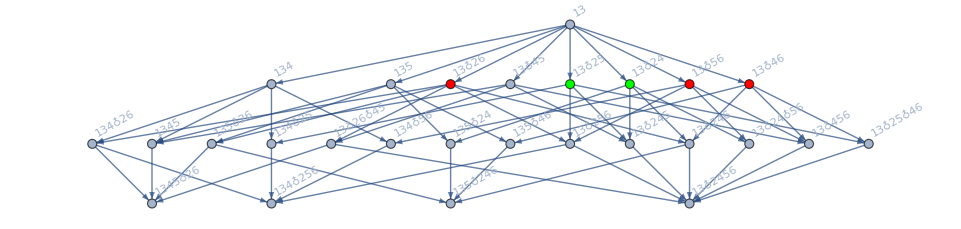

```mathematica
With[{g=FormulaGraphReverse2[allGraphs6Bis[8050374,"colofour"]]},
Graph[g,VertexStyle->
Join[
Map[ChangeSymbol[#,"v"]->Red&,Select[ListofVars[allGraphs6Bis[8050374,"colofour"]],SymbolLevel[#]==4&&HasQuadrilateralPattern[SymbolToSets[#]]&]],
Map[ChangeSymbol[#,"v"]->Green&,Select[ListofVars[allGraphs6Bis[8050374,"colofour"]],SymbolLevel[#]==4&&HasTrianglePattern[SymbolToSets[#]]&]]
]
]
]
```

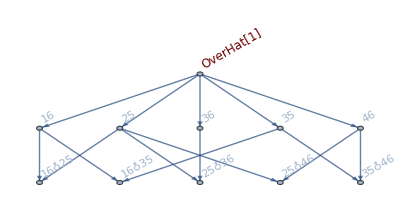

```mathematica
allGraphs6Bis[7113106,"colofour"]//FormulaGraphReverse2
```

```mathematica
Map[WhichQuadrilateralPattern[#]&,Map[SymbolToSets,Select[ListofVars[allGraphs6Bis[7113106,"colofourgenerator"]],SymbolLevel[#]==4&]]]
```

{4,1,4,4,1}